```mathematica
fold080916C="/Users/maxitg/Projects/GammaRays/GRObservations/DerivedData/GRObservations/Build/Products/Release/080916C/";
```

```mathematica
fold090902B="/Users/maxitg/Projects/GammaRays/GRObservations/DerivedData/GRObservations/Build/Products/Release/090902B/";
```

```mathematica
fold090926A="/Users/maxitg/Projects/GammaRays/GRObservations/DerivedData/GRObservations/Build/Products/Release/090926A/";
```

```mathematica
gevData=Import[fold090926A<>"gev","Table"];
```

```mathematica
mevData=Import[fold090926A<>"mev","Table"];
```

```mathematica
mevStretchedData=Import[fold090926A<>"stretchedMeV","Table"];
```

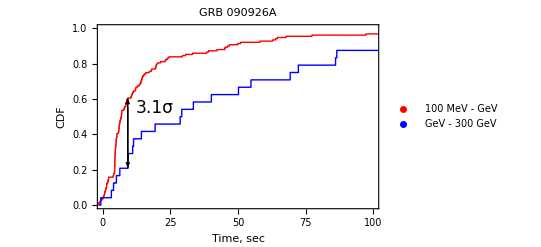

```mathematica
Show[
ListPlot[{mevData,gevData},Joined->True,PlotRange->{{0,100},Full},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","CDF"},LabelStyle->(FontSize->12),PlotLegends->Placed[{"100 MeV - GeV","GeV - 300 GeV"},{0.75,0.33}],PlotStyle->{Red,Blue},PlotLabel->"GRB 090926A"],
Graphics[{
Arrow[{{9.23659,0.208333+0.05},{9.23659,0.604931}}],
Arrow[{{9.23659,0.604931-0.05},{9.23659,0.208333}}],
Text[Style["3.1σ",FontSize->17],{12.23659,0.55},{-1,0}]
}]
]
```

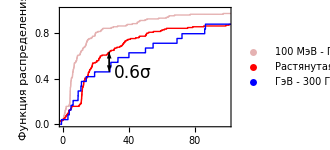

```mathematica
Show[
ListPlot[{mevData,mevStretchedData,gevData},Joined->True,PlotRange->{{0,100},Full},Frame->{{True,False},{True,False}},FrameLabel->{"Время, с","Функция распределения"},LabelStyle->(FontSize->12),PlotLegends->Placed[{"100 МэВ - ГэВ","Растянутая\n100 МэВ - ГэВ","ГэВ - 300 ГэВ"},{0.75,0.33}],PlotStyle->{{Opacity[0.3],Darker[Red]},Red,Blue}],
Graphics[{
Arrow[{{28.1904,0.508333},{28.1904,0.632432}}],
Arrow[{{28.1904,0.582432},{28.1904,0.458333}}],
Text[Style["0.6σ",FontSize->17],{31.1904,0.45},{-1,0}]
}]
]
```

```mathematica
InverseErf[0.5] √2
```

0.67449